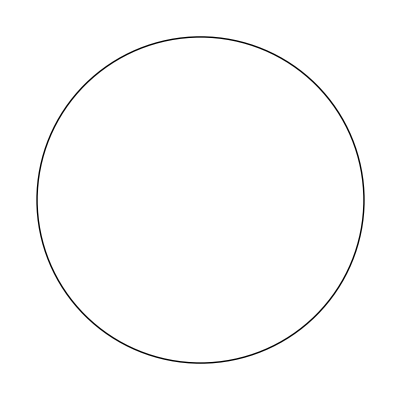

```mathematica
(* Caveat: Circle is invariant to rotational/mirroring transforms, which does not hold for other objects, which may point in oppposite directions (for mirroring transforms) *)
Graphics[GeometricTransformation[Circle[],AffineTransform[{{{-2,-50},{50,1}},{0,0}}]]]
```

```mathematica
{{2,1},{-50,-1}}//MatrixForm
```

(2 | 1
-50 | -1)